```mathematica
potentialValue=80.5;
l=25;

data = Dataset[{
<|"timeframe"->0.000001|>,
<|"timeframe"->0.00002|>,
<|"timeframe"->0.00003|>
}]


vacuumFluctuation[t_]=1/Sin[t] LegendreP[-(1/2)+I Sqrt[potentialValue - 9/4],l+1,Cos[t]];

firstDerivative[t_]=D[vacuumFluctuation[x],x]/.x->t;

logarithmicDerivative[t_]=firstDerivative[t]/vacuumFluctuation[t];

safeLogarithmicDerivative[t_]:=N@ReleaseHold[SetPrecision[Hold[logarithmicDerivative[t]],50]];

data=data[All,Append[#,"vacuum_fluctuation_logarithmic_derivative_mathematica"->safeLogarithmicDerivative[#timeframe]]&];

data
```

Failure[…]

```mathematica
safeLogarithmicDerivative[0.000001]
```

General::munfl: (2.50022×10^-13)^26 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::munfl: (2.50022×10^-13)^26 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Indeterminate

```mathematica
function[t_,V_,l_]:=N@ReleaseHold[SetPrecision[Hold[1/Sin[t]*LegendreP[-1/2+V*I,l+1,Cos[t]]],30]]
```

```mathematica
function[.00000001,10,50]
```

General::munfl: 1.342278837×10^-339+0. ⅈ is too small to represent as a normalized machine number; precision may be lost.

0.+0. ⅈ

```mathematica
Series[vacuumFluctuation[t], {t, π - 0.00001, 10}]
```

General::munfl: (20.4863+1.34227×10^-53 ⅈ) (4.14383×10^-265+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

-(2.50162×10^235-1.21984×10^236 ⅈ)-(2.50165×10^240-1.21987×10^241 ⅈ) (t-3.14158)-(2.50165×10^245-1.21987×10^246 ⅈ) (t-3.14158)^2-(2.50165×10^250-1.21987×10^251 ⅈ) (t-3.14158)^3-(2.50165×10^255-1.21987×10^256 ⅈ) (t-3.14158)^4-(2.50165×10^260-1.21987×10^261 ⅈ) (t-3.14158)^5-(2.50165×10^265-1.21987×10^266 ⅈ) (t-3.14158)^6-(2.50165×10^270-1.21987×10^271 ⅈ) (t-3.14158)^7-(2.50165×10^275-1.21987×10^276 ⅈ) (t-3.14158)^8-(2.50165×10^280-1.21987×10^281 ⅈ) (t-3.14158)^9-(2.50165×10^285-1.21987×10^286 ⅈ) (t-3.14158)^10+O[t-3.14158]^11

```mathematica
PadeApproximant[Normal[%19],{t,3.141582653589793,5}]
```

N::precsm: Requested precision -10.1278 is smaller than $MinPrecision. Using $MinPrecision instead.

((0.+0. ⅈ)-(7.92234×10^240-1.22664×10^241 ⅈ) (-3.14158+t)-(4.50153×10^245+9.90973×10^244 ⅈ) (-3.14158+t)^2-(3.04756×10^250+4.01913×10^249 ⅈ) (-3.14158+t)^3+(2.50156×10^255-1.21985×10^256 ⅈ) (-3.14158+t)^4+(2.50165×10^260-1.21987×10^261 ⅈ) (-3.14158+t)^5)/(0.+(109281.+42534.7 ⅈ) (-3.14158+t)-(1.09817×10^10+5.52339×10^8 ⅈ) (-3.14158+t)^2+(2.29076×10^13-1.23887×10^14 ⅈ) (-3.14158+t)^3-(1.01755×10^20+2.46226×10^19 ⅈ) (-3.14158+t)^4+(5.01012×10^19+1.87086×10^18 ⅈ) (-3.14158+t)^5)

```mathematica
InverseSeries[%19]
```

3.14158-(1.61328×10^-242+7.86677×10^-242 ⅈ) (t+(2.50162×10^235-1.21984×10^236 ⅈ))+O[t+(2.50162×10^235-1.21984×10^236 ⅈ)]^11

```mathematica
PhiTilde[t_] = Exp[Phi[t]];
```

```mathematica
D[PhiTilde[t], t]
```

Phi'[t]/Phi[t]

```mathematica
FullSimplify[D[D[PhiTilde[t], t], t]]
```

(-Phi'[t]^2+Phi[t] Phi''[t])/Phi[t]^2

```mathematica
ClearAll[l, s]
```

```mathematica
newODE = FullSimplify[-D[D[PhiTilde[t], t], t] - 3 * Cot[t] * D[PhiTilde[t], t] + (Vpp[t] + l*(l+2)/Sin[t]^2+s)PhiTilde[t]]
```

ⅇ^Phi[t] (s+l (2+l) Csc[t]^2+Vpp[t]-Phi'[t] (3 Cot[t]+Phi'[t])-Phi''[t])

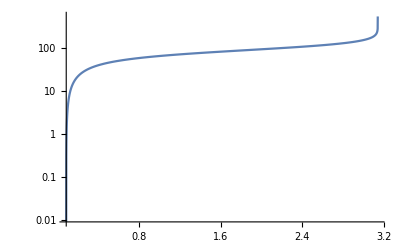

```mathematica
LogPlot[Log[vacuumFluctuation[t]], {t, 0, π}, PlotRange->All]
```

```mathematica
FullSimplify[Solve[newODE == 0, Phi''[t]]]
```

{{Phi''[t]→Log[Phi[t]] Phi[t] (s+l (2+l) Csc[t]^2+Vpp[t])-3 Cot[t] Phi'[t]+Phi'[t]^2/Phi[t]}}

```mathematica
Exp[10^10]
```

ⅇ^10000000000

```mathematica
N[ⅇ^10000000000]
```

1.077750607958564910057`5.954589770191001*^4342944819